## Plot Functions

```mathematica
pltLim[f_,rangex_:{x,0,10},origin_:{0,0}]:=
Module[{func=f},
ClearAll[lim];
imgSize=600;
lim=Limit[f,x->Infinity];
Plot[{f,lim},rangex,AxesOrigin->origin,PlotStyle->{Automatic,Dashed},ImageSize->imgSize,PlotLabel->f]
]
```

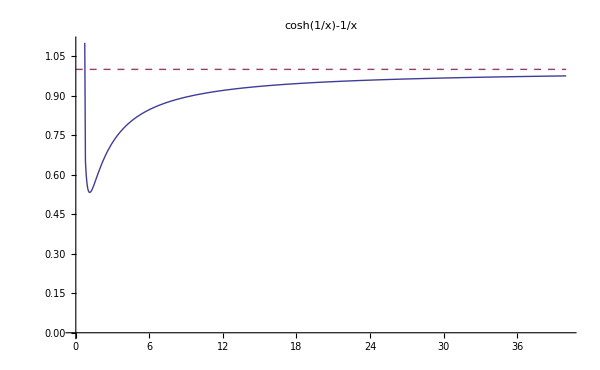

```mathematica
pltLim[Cosh[1/x]-1/x,{x,0,40},{0,0}]
```

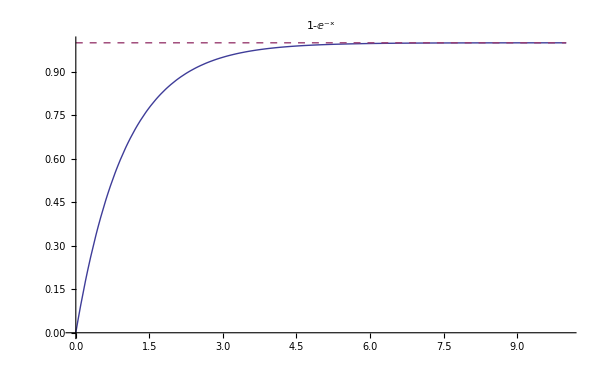

```mathematica
pltLim[1-Exp[-x],{x,0,10},{0,0}]
```

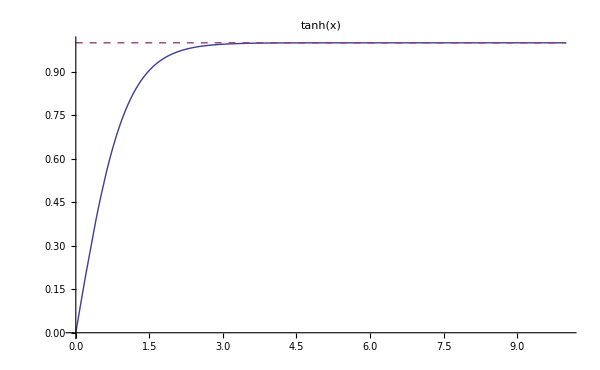

```mathematica
pltLim[Tanh[x],{x,0,10},{0,0}]
```

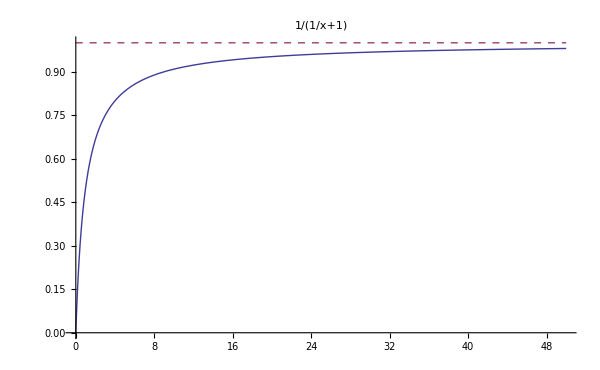

```mathematica
pltLim[1/(1+1/x),{x,0,50},{0,0}]
```

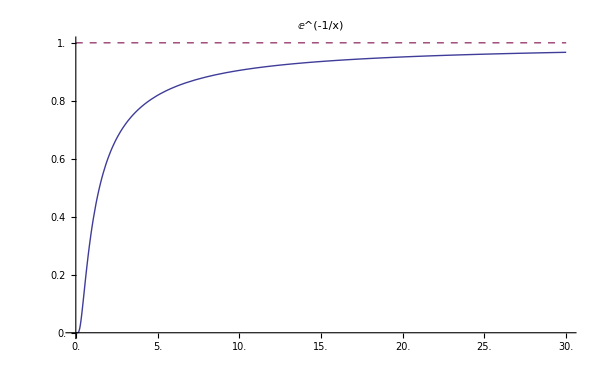
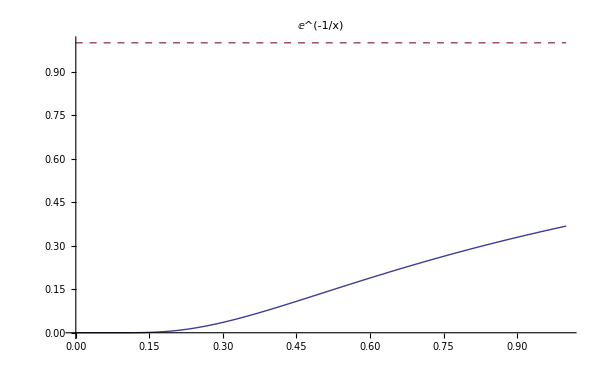

```mathematica
boltz1=pltLim[Exp[-1/x],{x,0,30},{0,0}];
boltz2=pltLim[Exp[-1/x],{x,0,1},{0,0}];

Graphics[{First[boltz1],Inset[boltz2,{18,.4},Automatic,Scaled[.6]]},AbsoluteOptions[boltz1]]
```

```mathematica
Series[ty[x],{x,0,3}]
```

ty[0]+ty'[0] x+1/2 ty''[0] x^2+1/6 ty^(3)[0] x^3+O[x]^4

```mathematica
Limit[D[Exp[-1/x],{x,100}],x->0]
```

0

For any integers n, we have

```mathematica
Limit[Exp[-1/x]/(x^n),x->0,Assumptions->n∈Integers]
```

0

So the nth derivative of this function is always 0 at x=0, for all finite n.